```mathematica
AllPathCanyons[g_,j_,i1_,i2_,i3_,i4_,l_,k_]:=Table[
Labeled[ArrayPlot[
Reverse@Transpose[
PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[i]],
{Automatic,Automatic},
.25
]
],
Frame->True,
ColorRules->{0->Hue[.95,.4,1.4],
1->Hue[.1,.1,.1]},
Mesh->True
],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]
|>]
],
{i,1,Length[VertexList[g]]}
]
```

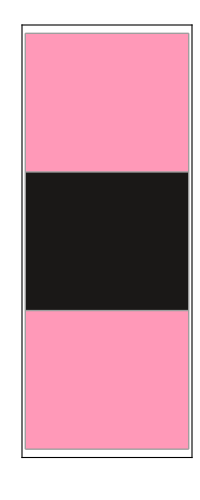
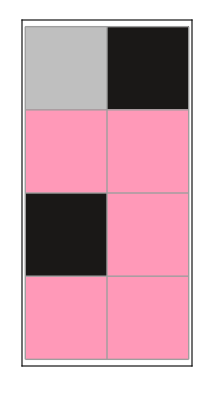
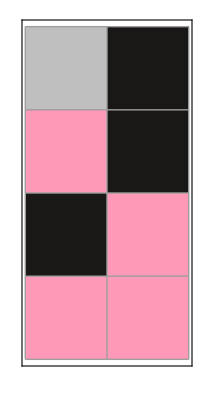
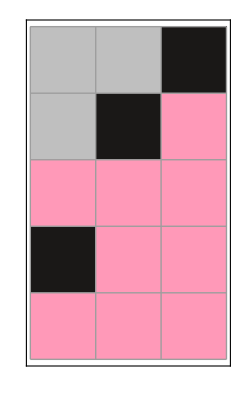
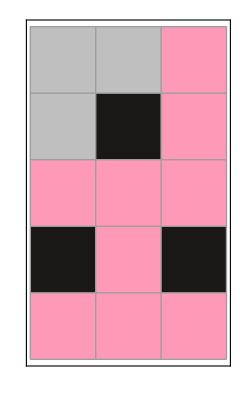
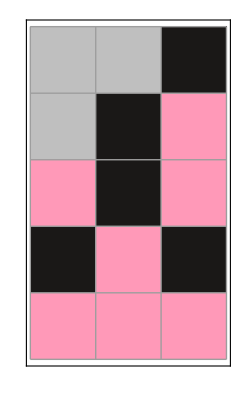
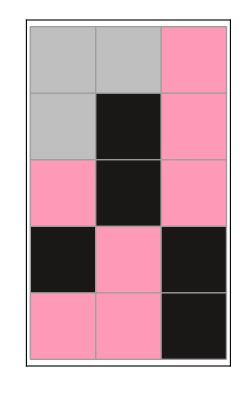
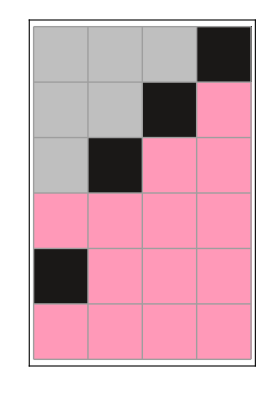
{{{{{{{{{-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1}}}}}},{{{{{-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1}}}}}},{{{{{-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1}}}}}},{{{{{-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{0, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1}}}}}},{{{{{-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1}}}}}},{{{{{-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 0, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1}}}}}},{{{{{-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 0}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1}}}}}},{{{{{-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1},-Graphics-{0,0,s___}->{1, 1, 1}
{1,0,s___}->{0, 1, 1}
{0,1,s___}->{0, 0, 1}
{1,1,s___}->{0, 0, 1}
{1, 1, 1}}}}}}}}}}

```mathematica
Table[Table[Table[Table[Table[
AllPathCanyons[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]
}],
{{0,1,0}},
4,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
],j,i1,i2,i3,i4,l,k],{t,5,5}],
{i1,1,2^j},
{i2,2^(j-1),2^(j-1)},
{i3,2^(j-2),2^(j-2)},
{i4,2^(j-2),2^(j-2)}],
{j,3,3}],
{k,2^l,2^l}],
{l,3,3}]
```

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[Table[
Column[Row/@PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[j]],
{Automatic,Automatic},
.25
],Center]//. 0.25->"",
{j,2,Length[VertexList[g]]}
]//.{x_}:>x],FontFamily->"Roboto"]
```

```mathematica
Table[
AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,1,0,0}],
{left___,1,0,s___}:>Flatten[{left,s,0,1}],
{left___,0,1,s___}:>Flatten[{left,s,1,1,0}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},2][[i]]}]
}],
{{1,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]],
{i,1,4}
]
```

{{11
00,11
00
100,11
00
100
001,11
00
100
1100,11
00
100
001
0110,11
00
100
1100
0000,11
00
100
1100
1001,11
00
100
1100
11100,11
00
100
1100
0000
00100,11
00
100
001
0110
0101,11
00
100
001
0110
10110,11
00
100
1100
11100
10000,11
00
100
1100
11100
11001,11
00
100
1100
11100
111100},{11
01,11
01
110,11
01
110
001,11
01
110
101,11
01
110
001
0110,11
01
110
001
1100,11
01
110
101
1110,11
01
110
001
0110
0001,11
01
110
001
0110
0101,11
01
110
001
0110
10110,11
01
110
001
1100
1001,11
01
110
001
1100
11100,11
01
110
101
1110
1101},{11
10,11
10
01,11
10
01
110,11
10
01
110
010,11
10
01
110
101,11
10
01
110
010
001,11
10
01
110
010
0110,11
10
01
110
101
1110},{}}